```mathematica
ClearAll["Global`*"]
```

```mathematica
xl=0;
xr=1;
```

```mathematica
(*test case 1*)
```

```mathematica
u[x_]:=Cos[x]Sin[x]
```

```mathematica
v[x_]:=u'[x]
```

```mathematica
u'''[x]//FullSimplify
```

-4 Cos[2 x]

```mathematica
(*check for u*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/third_order_pde/solution/u.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

```mathematica
δ=Max[Table[Abs[t[[i,2]]-u[t[[i,1]]]],{i,1,Length[t]}]]
```

6.10343×10^-8

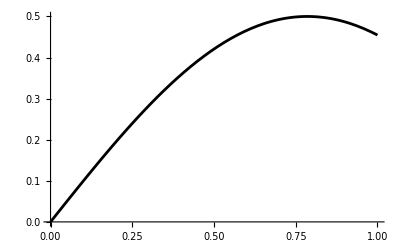

```mathematica
plotuexact=Plot[u[x],{x,xl,xr},PlotRange->Full,PlotStyle->Black]
```

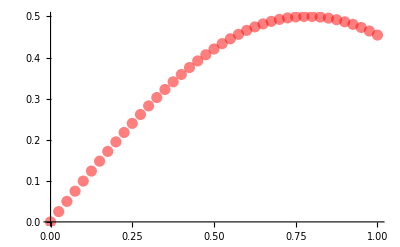

```mathematica
plotunum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[0.5],PointSize->0.02}]
```

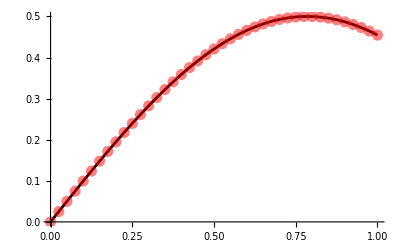

```mathematica
Show[plotuexact,plotunum]
```

```mathematica
(*check for v*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/third_order_pde/solution/v.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

```mathematica
δ=Max[Table[Abs[t[[i,2]]-v[t[[i,1]]]],{i,1,Length[t]}]]
```

5.58499×10^-9

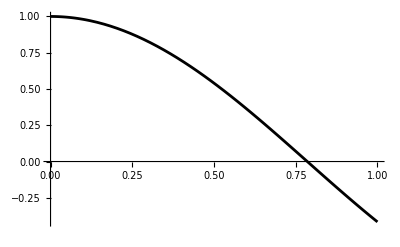

```mathematica
plotvexact=Plot[v[x],{x,xl,xr},PlotRange->Full,PlotStyle->Black]
```

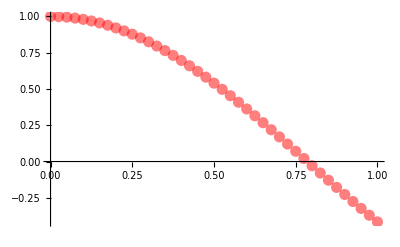

```mathematica
plotvnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[0.5],PointSize->0.02}]
```

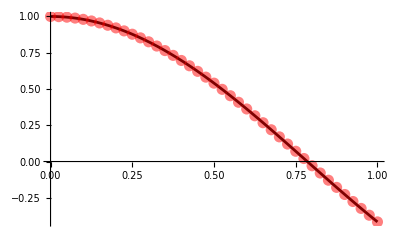

```mathematica
Show[plotvexact,plotvnum]
```